# Study When Different Turing Machines Compute the Same Function

In this essay, we say that setting a Turing machine to a nonnegative integer  refers to filling the cells of the tape between  and  for some specified  with the binary representation of  with the least significant bit at position . We ensure that  (the number of bits fits in ). Additionally, we say the value of a Turing machine is the number created by the binary digits from cells  to .

## Formalism

Let  be the set of all -state -color Turing machines. Each Turing machine in  represents a partial function  with input specified by the base  number formed by an interval  on the tape, where each color is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. 
1. Determine the cardinality of .
2. For each distinct function (equivalence class), determine and analyze the range of worst-case running times.

## Existing Work

We will begin by recreating the results shown on page 761 of Stephen Wolfram’s A New Kind of Science. Wolfram found that the space of all 2-state 2-color Turing machines represents exactly 351 distinct functions.

We will first create a function that simulates the evolution of a Turing machine with a tape set to some  with rule  until it reaches a halt state. Wolfram set the halt state as when the head to move to the right of its starting position (where the digits are not defined). Clearly, not all Turing machines will halt, so we will need to set a maximum iteration count. Also, for now, only four bit numbers will be used, which can represent numbers from 0 to 15.

Initialize rules and max iteration count:

```mathematica
states=2;
colors=2;
maxiters=64;
rules=Range[0,(2*states*colors)^(states*colors)-1];
bits=4;
width=11;
```

Using a smaller width allows less buffer space for the Turing machine to move past our defined interval  to give it a chance to return to . Wolfram used a width of 11 in NKS and I will use the smallest width possible of bits, which if 4. This is why our results diverge slightly. Note that results will be the same for width  6.

```mathematica
Length[rules]
```

4096

Why 4096 rules? For a -state -color Turing machine, there are  possible transitions, and for each transition there are  states to move to,  colors to change to, and 2 directions to move in, which results in a total of  machines. For , we have . This is why a generalized solution is difficult. For each increase of , the number of Turing machines increases exponentially by a factor of itself: enumeration is .

We set the initial condition to start in state 1 at position 11 of a tape of length 11 containing the value .

Set the initial condition as a function of :

```mathematica
init[n_]:={{1,width},{IntegerDigits[n,2,width],0}}
```

The Block body loops through the Turing machine evolution and checks for termination, which is passed to a Transpose block that trims the tape to only contain the first 11 colors. Since it loops through each stage of a Turing machine, it runs in approximately maxiters^2 time.

Stepping through the Turing machine evolution at every step is slower than generating it all at once even though there’s more symbols generated on average???

Compiled function to include and trim states until halt:

```mathematica
cfindhalt=Compile[
{{evols,_Integer,2},{width,_Integer}},
Block[{halt=False},
TakeWhile[
evols[[All,1;;3+width]],
Which[
halt,
False,
(*1-width<=*)#[[3]]<=0,(* valid position *)
True,
MatchQ[#[[3]],1(*|-width*)],(* halt position *)
halt=True
]&
]
],
CompilationTarget->"C",
RuntimeAttributes->{Listable}
];
```

Compiled hist function:

```mathematica
chist[rule_Integer, num_Integer]:=
cfindhalt[Flatten/@TuringMachine[{rule,states,colors},init[num],maxiters],width]
```

Example for rule 2237 starting on a tape of all zeros ().

```mathematica
Grid[
{#[[1;;3]],#[[4;;-1]]}&/@chist[2237,3],
Alignment->Left
]
```

{1,11,0} | {0,0,0,0,0,0,0,0,0,1,1}
{2,10,-1} | {0,0,0,0,0,0,0,0,0,1,0}
{2,11,0} | {0,0,0,0,0,0,0,0,0,1,0}
{2,12,1} | {0,0,0,0,0,0,0,0,0,1,0}

Now that we can get the full evolution of a Turing machine, we want to see the final result on termination for each of these machines. The function is shown below, which loops through each rule, then each number constrained by bits bits, and returning the final tape.

Get the final stage of evolution for each rule and number:

```mathematica
chist[2237,3]
```

{{1,11,0,0,0,0,0,0,0,0,0,0,1,1},{2,10,-1,0,0,0,0,0,0,0,0,0,1,0},{2,11,0,0,0,0,0,0,0,0,0,0,1,0},{2,12,1,0,0,0,0,0,0,0,0,0,1,0}}

```mathematica
cevol=Compile[
{{rule,_Integer},{bits,_Integer}},
Table[
With[{h=chist[rule,num]},
If[
h[[-1,3]]!=1,
-1,
FromDigits[h[[-1,2]],2]
]
],(* end With *)
{num,0,2^bits-1}
],
CompilationTarget->"C"
]
```

Compile::part: Part specification Compile`FunctionVariable$65404⟦-1,3⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::part: Part specification Compile`FunctionVariable$65404⟦-1,2⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

General::stop: Further output of Compile::part will be suppressed during this calculation.

CompiledFunction[…]

Call the function:

```mathematica
evols=getevols[bits,rules];
%[[2238]] (* final state of rule 2237 *)
```

{2237,{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14}}

The following two functions separate Turing machine equivalence classes into different groups.

Group rules by equivalence class and filter out non-terminating machines:

```mathematica
eqlgroups=
Map[
First,
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2]],{-1}]&
],
#[[2,2]]&
],
{2}
];
```

Number of groups:

```mathematica
Length[eqlgroups]
```

350

Group rules as above and additionally filter out unique machines:

```mathematica
multieqlgroups=
Map[
First,
Select[
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2]],{-1}]&
],
#[[2,2]]&
],
Length[#]>1&
],
{2}
];
```

For analysis purposes, multieqlgroups is more useful since we cannot say much about a Turing machine that is unique in what it does.

To measure the time complexity of each Turing machine, we are forced to do a brute-force simulation due to the Halting Problem.

Simulate the number of transitions until halt for all numbers of bits bits:

```mathematica
ht[rule_Integer,bits_Integer]:=
Select[
ParallelTable[
Block[{i=0,max=maxiters+1},(* 50 + 2n *)
NestWhile[
(i++;TuringMachine[{rule,states,colors},#])&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
(*1-width<=*)#[[1,3]]<=0&,(* stop when dx > 0, or when x < 1 - width *)
1,max
];
If[i==max,-1,i]
],
{n,1,2^bits-1}
],
#!=-1&
]
```

Halting configuration for rule 2238 for all 4 bit numbers:

```mathematica
ht[2237,bits]
```

{3,5,3,7,3,5,3,9,3,5,3,7,3,5,3}

To analyze the time complexity difference between each group of Turing machines, it is helpful to have explicit access to those values.

Get the 3-tuples for each group of Turing machines {min,max,range}

```mathematica
halttimes=Map[{#,ht[#,bits]}&,eqlgroups,{2}];
```

```mathematica
((Max@@#[[2]])&/@#)&/@halttimes; 
MinMax/@%;
haltdifs=Append[#,#[[2]]-#[[1]]]&/@%;
```

Combine each group into {tuple,{rules...},{{runtimes}...}}:

```mathematica
haltcombined=Transpose@{haltdifs,eqlgroups,halttimes[[All,All,2]]};
```

Sort by largest range: corresponding slow and fast Turing machines:

```mathematica
sortedmachines={#[[1]],Transpose[#[[2;;3]]]}&/@SortBy[haltcombined,-#[[1,-1]]&];
```

```mathematica
list=Transpose@{sortedmachines[[All,1]],sortedmachines[[All,2,All,1]]};
```

Number of unique functions (equivalence classes):

```mathematica
Length@list[[All,2]]
```

350

List of the number of Turing machines in each  equivalence class:

```mathematica
Length@#[[2]]&/@list
```

{280,273,19,3,119,4,6,119,6,5,6,2,2,3,5,5,8,99,2,5,99,2,6,2,5,2,2,3,4,8,9,3,5,6,9,6,261,269,4,4,6,6,8,8,9,9,11,11,12,12,14,14,19,19,3,2,2,4,4,4,17,2,3,4,4,4,17,226,226,232,232,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,8,8,11,11,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,3,3,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,3,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

### POTENTIALLY OUTDATED SECTION

The number of unique functions 351 we found here is the same number Wolfram found in NKS (Wolfram, 759).

Find the last group (it turns out) of size 17 and see the outputs:

```mathematica
Length@#[[2]]&/@list;
Position[%,17,-1][[2,1]];
If[%!=-1,evols[[list[[%,2,1]]+1,2]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

## Distribution Analysis

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
```

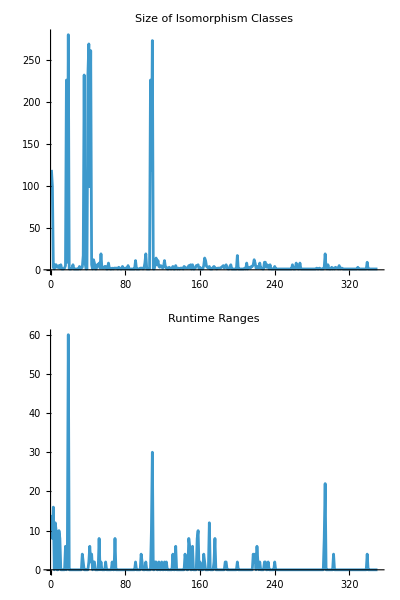

```mathematica
Column[With[{w=1600},{
ListPlot[
Length/@eqlgroups,
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes"
],
ListPlot[
haltdifs[[All,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Runtime Ranges"
]
}]]
```

Generally, spikes in the size of equivalence classes, aside from the first, generally corresponds to spikes in runtime range, yet there are also some spikes where there is low runtime range.
Spikes in runtime ranges are more frequent. Some spikes correspond with large equivalence classes, but there is a spike at group 295 where the size is very small. Large runtime ranges also happen during the large size spike in the beginning.

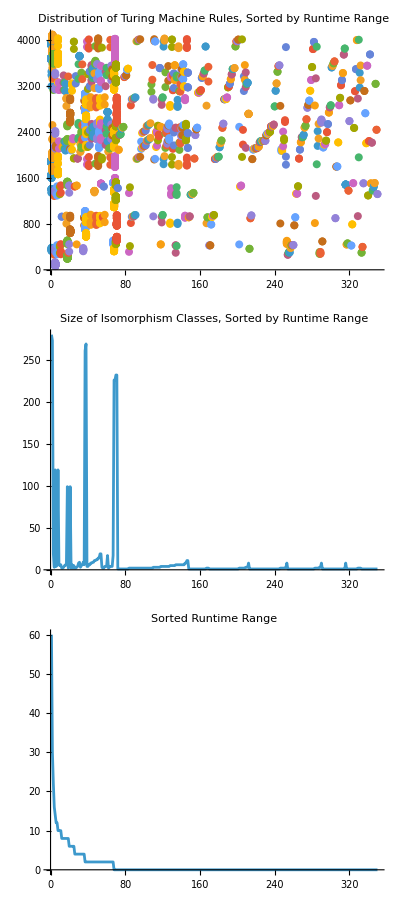

```mathematica
Column[With[{w=1600},{
ListPlot[
stackPoints[list[[All,2]]],
PlotRange->Full,
ImageSize->{w,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of Turing Machine Rules, Sorted by Runtime Range"
],
ListPlot[
Length/@list[[All,2]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes, Sorted by Runtime Range"
],
ListPlot[
list[[All,1,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/8,
PlotLabel->"Sorted Runtime Range"
]
}]]
```

larger groups of isomorphic rules generally correspond to a larger difference so we only pick the large groups??

## Pruning

```mathematica
n=states;
k=colors;
```

Define the function  to be the number of permutations of the output states in each rule without permuting the first  pairs of states. Note that  is defined for all rational numbers that is an integer divided by .
Define  to be the starting rule number corresponding to a configuration that begins with .

### Contiguous Intervals

The length of each continuous interval of isomorphic rule sets has length of  where  is the degree of the rule sets.

```mathematica
perm[d_]:=IntegerPart[(2*n*k)^(k*(n-d))]
mkitv[r_,i_,d_]:=r+{(i-1)*perm[d],i*perm[d]}
mkitv[r_,d_]:=r+{0,2*k*perm[d]}
```

Trivially, , and the length of each interval is . For a degree 1 configuration, we have two intervals starting at  and .

```mathematica
S11=0;
mkitv[S11,1]
mkitv[S11+perm[0.5],1]
```

{0,256}

{512,768}

For each of these intervals, they are split into  subintervals since each permutation of direction and color changes the behavior of the Turing machine. The mkitv[r_,i_,d_]is to get the th of these intervals.

because we need to permute the last block to increase the state in front of it. In general, to increment a state at position , it will take  permutations.

```mathematica
S12=2*k*perm[1];
```

In this case, . Thus we have the following three intervals.

First trivial interval at :

```mathematica
mkitv[S12,2]
```

{256,260}

Interval at :

```mathematica
mkitv[S12+2*k*perm[2],2]
```

{260,264}

Interval at :

```mathematica
mkitv[S12+2*k*perm[1.5],2]
```

{288,292}

Interval at :

```mathematica
mkitv[S12+2*k*(perm[1.5]+perm[2]),2]
```

{292,296}

### State Transition Graph Pruning (TODO: use intervals in previous section)

We define an unreachable state to be a state that will never be reached by the Turing machine following a specified rule. Similarly, a reachable state is a state that can be reached by a Turing machine through a finite number of transitions. 

Pruning unreachable states can also be done by analyzing the connectivity of a rule’s state transition graph. The vertices of this graph represents the possible states the Turing machine can be in, and edges represent state transitions specified by the rule. Note that we do not need to store data alongside an edge. However, for each reachable state, we need to distinguish between the direction and color of each transition. Formally, given that  is reachable, for a transition , we must distinguish between all  permutations of  and  for a fixed resulting state .

Let us construct a function that produces a comparable identifier to check if two rules are isomorphic. To group permutations of unreachable states, we can simply remove them from the identifier.

Get the rule identifier and the state transition graph for a specified rule :

```mathematica
getinfo[r_]:={
Flatten@Transpose@{r[[All,1,2]],r[[All,2]]},
Graph[
r[[All,All,1]],
VertexLabels->Automatic
]
}
```

Te function above takes in a list of rules with each rule in the form , so we use the following resource function to get the canonical rule form from the rule number.

Get resource function:

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
```

Get canonical form of all possible rules:

```mathematica
n=3;
k=2;
(2*n*k)^(n*k)
rules=ParallelMap[tmRuleFromNum[#,n,k]&,Range[0,%-1]];
```

2985984

Example diagram for rule 0:

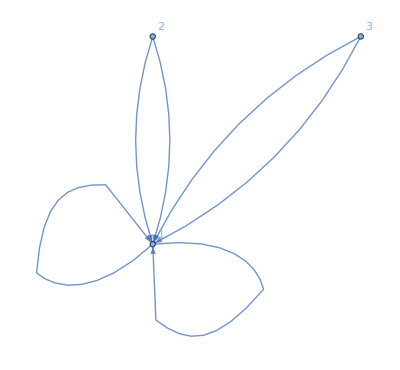
{{1,1,0,-1,0,1,0,-1,1,1,0,-1,0,1,0,-1,1,1,0,-1,0,1,0,-1},-Graphics-}

```mathematica
getinfo[rules[[1]]]
```

As mentioned, the way the identifier from getinfo is designed is for isomorphic rules to return the same identifier. As we iterate through rules, we maintain a counter for each identifier encountered using a hash table. Then for each rule, we build a state graph, determine which states are reachable from state (vertex) 1 using VertexOutComponent, and increment its associated identifier.

Note that the best we can do is to iterate through every rule, since the interleaved configuration of isomorphic rules necessitates iteration even if we know which ones are isomorphic ahead of time.

Compile the transformation function to get rule identifier:

```mathematica
ctransform=Compile[
{{reachable,_Integer,2},{info,_Integer,2}},
(* begin fn *)
Table[
Join@@
Table[
If[
MemberQ[reachable[[i]],j],
Flatten@info[[i,6*j-5;;6*j]],
ConstantArray[1,6]
],
{j,n}
],(* end Table over j *)
{i,Length[info]}
](* end Table over i *),
(* end fn *)
CompilationTarget->"C",
RuntimeAttributes->{Listable}
];
```

Update the hash table map by pruning the rules specified by the rules list:

```mathematica
prune[map_DataStructure,rules_List]:=
Block[
{info=getinfo/@rules,reachables,transL},
reachables=PadLeft[VertexOutComponent[#,{1}],3,-1]&/@info[[All,2]];
transL=ctransform[
reachables,
Partition[Flatten[info[[All,1,All,2]]],3*n*k]
];
map["Insert",(#->map["Lookup",#,0&]+1)]&/@transL;(*sequential*)
]
```

Initialize the hash table and call the function:

```mathematica
map=CreateDataStructure["HashTable"];
prune[map,rules]
```

Check the size of the map (we only need to check this many Turing machines):

```mathematica
elems=map["Elements"];
Length[%]
```

1775632

## Search

Now that we have applied DFA minimization, I could not find any more algorithmic cleverness we can do to reduce the search space; rather, I conjecture that this is the best we can do. 

Rice’s theorem, a generalization of the undecidability of the Halting problem, states that non-trivial semantic properties of programs are undecidable, directly causing there to be no general way to analyze the behavior of a Turing machine (http://kilby.stanford.edu/~rvg/154/handouts/Rice.html and wikipedia). There is a simple explanation for this. Suppose  is an arbitrary Turing machine and suppose the Halting Problem is decidable. Then define machine  such that it simulates  on some input  and returns some function if it halts and  otherwise. Checking if  computes  or  on  is the same as checking if  halts, which is undecidable, thus necessitating the decidability of an undecidable problem.

Consequently, this section will be mainly compiling to C and micro-optimizing brute-force.

rulesCompressed, ruleNumsCompressed, and ruleRepeats should be parallel lists.

Get the number of times each rule is repeated:

```mathematica
ruleRepeats=elems[[All,2]]
```

Reconstruct rules from their hash table key form along with their number of occurrences:

```mathematica
ruleSpecs=With[
{
key=Transpose@{
Riffle[Range[n],Range[n]],
Table[BitAnd[i,1],{i,n*k}]
},
vals=Partition[#[[1]],3]&/@elems
},
Transpose@{
ParallelMap[Table[key[[i]]->#[[i]],{i,n*k}]&,vals],
ruleRepeats
}
];
```

Convert to rule numbers:

```mathematica
ruleNumsCompressed=tmRuleToNum[#][[1]]&/@ruleSpecs[[All,1]];
```

Since many of the Turing machine simulation operations are data processing, we can leverage the C compiler with Compile to speed up code significantly.

Compile functions to speed up getevols

```mathematica
chist[rule_Integer, num_Integer]:=cfindhalt[Flatten/@TuringMachine[{rule,n,k},init[num],maxiters],width]
```

```mathematica
getlast[rule_Integer,bits_Integer]:=
ParallelTable[
With[{h=chist[rule,num]},
If[
h[[-1,3]]!=1,
-1,
FromDigits[h[[-1,4;;-1]],2]
]
],(* end With *)
{num,0,2^bits-1}
]
```

```mathematica
cevol=Compile[
{{rule,_Integer},{bits,_Integer}},
getlast[rule,bits],
{{getlast[_,_],_Integer,1}},
CompilationTarget->"C",
RuntimeAttributes->{Listable},
Parallelization->True
];
```

```mathematica
cgetevols=Compile[
{{bits,_Integer},{rules,_Integer,1}},
cevol[#,bits]&/@rules,
CompilationTarget->"C",
RuntimeAttributes->{Listable},
Parallelization->True
];
```

This is by far the most computationally expensive function, which took 1.5 hours to run.

Evolve the compressed rules only:

```mathematica
evols=getevols[bits,ruleNumsCompressed];
```

Group rules by equivalency:

```mathematica
eqlgroups=
Map[
First,
GatherBy[
Select[
Thread[Join[ruleRepeats,evols]],
!ContainsOnly[#[[2]],{-1}]&
],
#[[2]]&
],
{2}
];
```

```mathematica
multieqlgroups=
Map[
First,
Select[
GatherBy[
Select[
Thread[Join[ruleRepeats,evols]],
!ContainsOnly[#[[2]],{-1}]&
],
#[[2]]&
],
Length[#]>1&
],
{2}
];
```

```mathematica
Length[eqlgroups]
```

Simulating a Turing machine is usually computationally irreducible, but since we are operating on a fixed, finite tape, we can cache each evolution of the Turing machine. If a cached evolution is encountered, we can assume that the machine will not halt. Additionally, we can store all evolution states that do not halt into a global hash set to be used in subsequent computations. (credit: gregory)

Global DP table:

```mathematica
dpGlobal=CreateDataStructure["HashSet"];
```

Get halt times:

```mathematica
htDP[rule_Integer,bits_Integer]:=
ParallelTable[
Block[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",0],
max=50+2^(Log2[n+1]),(* 50 + 2n *)
tm,
tmp,
flag
},
NestWhile[
(
i["Increment"];
tm=TuringMachine[rule,#];
tmp=Flatten[tm];
If[
!(flag=dpGlobal["MemberQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpGlobal["Insert",tmp],
dp["Insert",tmp->1]
]
];
tm
)&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
!flag||1-width<=#[[1,3]]<=0&,
1,max
];
If[i["Get"]==max,0,i["Get"]]
],
{n,1,2^bits-1}
]
```

Result for rule 2237:

```mathematica
htDP[2237,4]
```

Get halt times

```mathematica
halttimes=Map[{#,ht[#,bits]}&,eqlgroups,{2}];
```